```mathematica
Clear["Global`*"];
```

## Example 3 of Phys. Rev. E 107, 035306

### Definitions

```mathematica
sz=PauliMatrix[3];sminus =  {{0,0},{1,0}};L1=sminus;H=h*sz/2;
```

### Computing p and q

```mathematica
Lindb[A_]:=-ⅈ(A.H-H.A) +γ*L1.A.ConjugateTranspose[L1]-(γ/2)*( ConjugateTranspose[L1].L1.A+A.ConjugateTranspose[L1].L1 ) ;
B=Table[PauliMatrix[i]/√2,{i,{4,1,2,3}}]; 
(*Este es el orden de la base del paper: I,x,y,z*)
L = Simplify[Table[Tr[B[[i]].Lindb[B[[j]]]],{i,1,4},{j,1,4}]]*Δt;
F= MatrixExp[L];
S = Table[Sum[F[[s,r]]*Tr[B[[r]].B[[a]].B[[s]].B[[b]]],{s,1,4},{r,1,4}],{a,1,4},{b,1,4}];
Kraus[X_] :=Sum[S[[a,b]]*(B[[a]].X.B[[b]]),{a,1,4},{b,1,4}] ;
W=FullSimplify[ Table[Tr[B[[i]].Kraus[B[[j]]]],{i,1,4},{j,1,4}],{h>0,Δt>0,γ>0}];
p = W[[2;;4,2;;4]];
q = W[[2;;4,1]];
p//MatrixForm
q//MatrixForm
```

(ⅇ^(-(γ Δt)/2) Cos[h Δt] | ⅇ^(-(γ Δt)/2) Sin[h Δt] | 0
-ⅇ^(-(γ Δt)/2) Sin[h Δt] | ⅇ^(-(γ Δt)/2) Cos[h Δt] | 0
0 | 0 | ⅇ^(-γ Δt))

(0
0
-1+ⅇ^(-γ Δt))

### Computing the derivatives of p and q

```mathematica
dp = D[p,h];
dq = D[q,h];
MatrixForm[dp]MatrixForm[dq]
```

(0
0
0) (-ⅇ^(-(γ Δt)/2) Δt Sin[h Δt] | ⅇ^(-(γ Δt)/2) Δt Cos[h Δt] | 0
-ⅇ^(-(γ Δt)/2) Δt Cos[h Δt] | -ⅇ^(-(γ Δt)/2) Δt Sin[h Δt] | 0
0 | 0 | 0)

### Computing the fixed point x

```mathematica
D1=2;
D2=4;
ρ=Table[f[i,j],{i,D1},{j,D1}];
```

#### Computing the eigenvalues to take the one with zero value

```mathematica
Ltotal=Chop[-ⅈ(ρ.H-H.ρ) +γ*L1.ρ.ConjugateTranspose[L1]-(γ/2)*( ConjugateTranspose[L1].L1.ρ+ρ.ConjugateTranspose[L1].L1 ) ];
Do[Do[f[i,j]=Table[KroneckerDelta[(i-1) *D1+ j,k],{k,D2}],{j,D1}],{i,D1}];
Liouvillian=FullSimplify[Flatten[Ltotal,1]];
righteig=Chop[Eigenvectors[Liouvillian]];
Ei=Chop[Eigensystem[Liouvillian][[1]]];
index =FirstPosition[Ei,0];
```

#### Computing the x vector of the fixed point

```mathematica
w=Chop[righteig[[index[[1]]]]];
cont=1; (*variable contador*)
ρsteady=ConstantArray[0,{D1,D1}];
Do[ρsteady[[i,j]]= w[[cont]];cont=cont+1 ,{i,D1},{j,D1}];
ρsteady=FullSimplify[ρsteady/Tr[ρsteady],{h>0,γ>0}];
x = Sqrt[2]*Table[Tr[B[[i]].ρsteady],{i,1,4}][[2;;4]];
MatrixForm[ρsteady]MatrixForm[x]
```

(0 | 0
0 | 1) (0
0
-1)

### Evaluating the Proposition

```mathematica
SI = dp.x+dq;
MatrixForm[SI]
```

(0
0
0)

## Example 2 of Phys. Rev. E 107, 035306

### Definitions

```mathematica
sz=PauliMatrix[3]; sx=PauliMatrix[1];L1=sz;H=h*sx/2;
```

### Computing p and q

```mathematica
Lindb[A_]:=-ⅈ(A.H-H.A) +γ*L1.A.ConjugateTranspose[L1]-(γ/2)*( ConjugateTranspose[L1].L1.A+A.ConjugateTranspose[L1].L1 ) ;
B=Table[PauliMatrix[i]/√2,{i,{4,1,2,3}}]; 
(*Este es el orden de la base del paper: I,x,y,z*)
L = Simplify[Table[Tr[B[[i]].Lindb[B[[j]]]],{i,1,4},{j,1,4}]]*Δt;
F= MatrixExp[L];
S = Table[Sum[F[[s,r]]*Tr[B[[r]].B[[a]].B[[s]].B[[b]]],{s,1,4},{r,1,4}],{a,1,4},{b,1,4}];
Kraus[X_] :=Sum[S[[a,b]]*(B[[a]].X.B[[b]]),{a,1,4},{b,1,4}] ;
W=FullSimplify[ Table[Tr[B[[i]].Kraus[B[[j]]]],{i,1,4},{j,1,4}],{h>0,Δt>0,γ>0}];
p = W[[2;;4,2;;4]];
q = W[[2;;4,1]];
p//MatrixForm
q//MatrixForm
```

(ⅇ^(-2 γ Δt) | 0 | 0
0 | ⅇ^(-γ Δt) (Cosh[√(-h^2+γ^2) Δt]-(γ Sinh[√(-h^2+γ^2) Δt])/(√(-h^2+γ^2))) | (ⅇ^(-γ Δt) h Sinh[√(-h^2+γ^2) Δt])/(√(-h^2+γ^2))
0 | -(ⅇ^(-γ Δt) h Sinh[√(-h^2+γ^2) Δt])/(√(-h^2+γ^2)) | ⅇ^(-γ Δt) (Cosh[√(-h^2+γ^2) Δt]+(γ Sinh[√(-h^2+γ^2) Δt])/(√(-h^2+γ^2))))

(0
0
0)

### Computing the derivatives of p and q

```mathematica
dp = D[p,h];
dq = D[q,h];
MatrixForm[dp]MatrixForm[dq]
```

(0
0
0) (0 | 0 | 0
0 | ⅇ^(-γ Δt) ((h γ Δt Cosh[√(-h^2+γ^2) Δt])/(-h^2+γ^2)-(h γ Sinh[√(-h^2+γ^2) Δt])/((-h^2+γ^2)^(3/2))-(h Δt Sinh[√(-h^2+γ^2) Δt])/(√(-h^2+γ^2))) | -(ⅇ^(-γ Δt) h^2 Δt Cosh[√(-h^2+γ^2) Δt])/(-h^2+γ^2)+(ⅇ^(-γ Δt) h^2 Sinh[√(-h^2+γ^2) Δt])/((-h^2+γ^2)^(3/2))+(ⅇ^(-γ Δt) Sinh[√(-h^2+γ^2) Δt])/(√(-h^2+γ^2))
0 | (ⅇ^(-γ Δt) h^2 Δt Cosh[√(-h^2+γ^2) Δt])/(-h^2+γ^2)-(ⅇ^(-γ Δt) h^2 Sinh[√(-h^2+γ^2) Δt])/((-h^2+γ^2)^(3/2))-(ⅇ^(-γ Δt) Sinh[√(-h^2+γ^2) Δt])/(√(-h^2+γ^2)) | ⅇ^(-γ Δt) (-(h γ Δt Cosh[√(-h^2+γ^2) Δt])/(-h^2+γ^2)+(h γ Sinh[√(-h^2+γ^2) Δt])/((-h^2+γ^2)^(3/2))-(h Δt Sinh[√(-h^2+γ^2) Δt])/(√(-h^2+γ^2))))

### Computing the fixed point x

```mathematica
D1=2;
D2=4;
ρ=Table[f[i,j],{i,D1},{j,D1}];
```

#### Computing the eigenvalues to take the one with zero value

```mathematica
Ltotal=Chop[-ⅈ(ρ.H-H.ρ) +γ*L1.ρ.ConjugateTranspose[L1]-(γ/2)*( ConjugateTranspose[L1].L1.ρ+ρ.ConjugateTranspose[L1].L1 ) ];
Do[Do[f[i,j]=Table[KroneckerDelta[(i-1) *D1+ j,k],{k,D2}],{j,D1}],{i,D1}];
Liouvillian=FullSimplify[Flatten[Ltotal,1]];
righteig=Chop[Eigenvectors[Liouvillian]];
Ei=Chop[Eigensystem[Liouvillian][[1]]];
index =FirstPosition[Ei,0];
```

#### Computing the x vector of the fixed point

```mathematica
w=Chop[righteig[[index[[1]]]]];
cont=1; (*variable contador*)
ρsteady=ConstantArray[0,{D1,D1}];
Do[ρsteady[[i,j]]= w[[cont]];cont=cont+1 ,{i,D1},{j,D1}];
ρsteady=FullSimplify[ρsteady/Tr[ρsteady],{h>0,γ>0}];
x = Sqrt[2]*Table[Tr[B[[i]].ρsteady],{i,1,4}][[2;;4]];
MatrixForm[ρsteady]MatrixForm[x]
```

(1/2 | 0
0 | 1/2) (0
0
0)

### Evaluating the Proposition

```mathematica
SI = dp.x+dq;
MatrixForm[SI]
```

(0
0
0)

## “A properly engineered QRC system” of Phys. Rev. E 107, 035306

### Definitions

```mathematica
sx=PauliMatrix[1];sminus =  {{0,0},{1,0}};L1=sminus;H=h*sx/2;
```

### Computing p and q

```mathematica
Lindb[A_]:=-ⅈ(A.H-H.A) +γ*L1.A.ConjugateTranspose[L1]-(γ/2)*( ConjugateTranspose[L1].L1.A+A.ConjugateTranspose[L1].L1 ) ;
B=Table[PauliMatrix[i]/√2,{i,{4,1,2,3}}]; 
(*Este es el orden de la base del paper: I,x,y,z*)
L = Simplify[Table[Tr[B[[i]].Lindb[B[[j]]]],{i,1,4},{j,1,4}]]*Δt;
F= MatrixExp[L];
S = Table[Sum[F[[s,r]]*Tr[B[[r]].B[[a]].B[[s]].B[[b]]],{s,1,4},{r,1,4}],{a,1,4},{b,1,4}];
Kraus[X_] :=Sum[S[[a,b]]*(B[[a]].X.B[[b]]),{a,1,4},{b,1,4}] ;
W=FullSimplify[ Table[Tr[B[[i]].Kraus[B[[j]]]],{i,1,4},{j,1,4}],{h>0,Δt>0,γ>0}];
p = W[[2;;4,2;;4]];
q = W[[2;;4,1]];
MatrixForm[p]MatrixForm[q]
```

(0
(ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h (-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) γ (-4 h+γ) (4 h+γ)-3 γ^2 √(-16 h^2+γ^2)+3 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) γ^2 √(-16 h^2+γ^2)+(1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) (-16 h^2 γ+γ^3)))/((-4 h+γ) (4 h+γ) (2 h^2+γ^2))
(ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) (γ^3 ((1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) γ-(-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) √(-16 h^2+γ^2))-8 h^2 γ (2 (1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) γ+(-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) √(-16 h^2+γ^2))))/(2 (-32 h^4-14 h^2 γ^2+γ^4))) (ⅇ^(-(γ Δt)/2) | 0 | 0
0 | ⅇ^(-(3 γ Δt)/4) (Cosh[1/4 √(-16 h^2+γ^2) Δt]+(γ Sinh[1/4 √(-16 h^2+γ^2) Δt])/(√(-16 h^2+γ^2))) | (4 ⅇ^(-(3 γ Δt)/4) h Sinh[1/4 √(-16 h^2+γ^2) Δt])/(√(-16 h^2+γ^2))
0 | -(4 ⅇ^(-(3 γ Δt)/4) h Sinh[1/4 √(-16 h^2+γ^2) Δt])/(√(-16 h^2+γ^2)) | ⅇ^(-(3 γ Δt)/4) (Cosh[1/4 √(-16 h^2+γ^2) Δt]-(γ Sinh[1/4 √(-16 h^2+γ^2) Δt])/(√(-16 h^2+γ^2))))

### Computing the derivatives of p and q

```mathematica
dp = D[p,h];
dq = D[q,h];
MatrixForm[dp]MatrixForm[dq]
```

(0
-(4 ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h^2 (-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) γ (-4 h+γ) (4 h+γ)-3 γ^2 √(-16 h^2+γ^2)+3 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) γ^2 √(-16 h^2+γ^2)+(1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) (-16 h^2 γ+γ^3)))/((-4 h+γ) (4 h+γ) (2 h^2+γ^2)^2)-(4 ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h (-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) γ (-4 h+γ) (4 h+γ)-3 γ^2 √(-16 h^2+γ^2)+3 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) γ^2 √(-16 h^2+γ^2)+(1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) (-16 h^2 γ+γ^3)))/((-4 h+γ) (4 h+γ)^2 (2 h^2+γ^2))+(4 ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h (-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) γ (-4 h+γ) (4 h+γ)-3 γ^2 √(-16 h^2+γ^2)+3 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) γ^2 √(-16 h^2+γ^2)+(1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) (-16 h^2 γ+γ^3)))/((-4 h+γ)^2 (4 h+γ) (2 h^2+γ^2))+(ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) (-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) γ (-4 h+γ) (4 h+γ)-3 γ^2 √(-16 h^2+γ^2)+3 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) γ^2 √(-16 h^2+γ^2)+(1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) (-16 h^2 γ+γ^3)))/((-4 h+γ) (4 h+γ) (2 h^2+γ^2))+(4 ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h^2 (-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) γ (-4 h+γ) (4 h+γ)-3 γ^2 √(-16 h^2+γ^2)+3 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) γ^2 √(-16 h^2+γ^2)+(1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) (-16 h^2 γ+γ^3)) Δt)/((-4 h+γ) (4 h+γ) √(-16 h^2+γ^2) (2 h^2+γ^2))+(ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h (-32 (1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) h γ-8 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) γ (-4 h+γ)+8 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) γ (4 h+γ)+(48 h γ^2)/(√(-16 h^2+γ^2))-(48 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) h γ^2)/(√(-16 h^2+γ^2))-24 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) h γ^2 Δt+(8 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h γ (-4 h+γ) (4 h+γ) Δt)/(√(-16 h^2+γ^2))-(8 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) h (-16 h^2 γ+γ^3) Δt)/(√(-16 h^2+γ^2))))/((-4 h+γ) (4 h+γ) (2 h^2+γ^2))
-(ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) (-128 h^3-28 h γ^2) (γ^3 ((1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) γ-(-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) √(-16 h^2+γ^2))-8 h^2 γ (2 (1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) γ+(-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) √(-16 h^2+γ^2))))/(2 (-32 h^4-14 h^2 γ^2+γ^4)^2)+(2 ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h (γ^3 ((1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) γ-(-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) √(-16 h^2+γ^2))-8 h^2 γ (2 (1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) γ+(-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) √(-16 h^2+γ^2))) Δt)/(√(-16 h^2+γ^2) (-32 h^4-14 h^2 γ^2+γ^4))+(ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) (-16 h γ (2 (1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) γ+(-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) √(-16 h^2+γ^2))+γ^3 ((16 (-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) h)/(√(-16 h^2+γ^2))+8 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) h Δt+γ (-(8 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) h Δt)/(√(-16 h^2+γ^2))+(8 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h Δt)/(√(-16 h^2+γ^2))))-8 h^2 γ (-(16 (-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) h)/(√(-16 h^2+γ^2))-8 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) h Δt+2 γ (-(8 ⅇ^(1/2 √(-16 h^2+γ^2) Δt) h Δt)/(√(-16 h^2+γ^2))+(8 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h Δt)/(√(-16 h^2+γ^2))))))/(2 (-32 h^4-14 h^2 γ^2+γ^4))) (0 | 0 | 0
0 | ⅇ^(-(3 γ Δt)/4) (-(4 h γ Δt Cosh[1/4 √(-16 h^2+γ^2) Δt])/(-16 h^2+γ^2)+(16 h γ Sinh[1/4 √(-16 h^2+γ^2) Δt])/((-16 h^2+γ^2)^(3/2))-(4 h Δt Sinh[1/4 √(-16 h^2+γ^2) Δt])/(√(-16 h^2+γ^2))) | -(16 ⅇ^(-(3 γ Δt)/4) h^2 Δt Cosh[1/4 √(-16 h^2+γ^2) Δt])/(-16 h^2+γ^2)+(64 ⅇ^(-(3 γ Δt)/4) h^2 Sinh[1/4 √(-16 h^2+γ^2) Δt])/((-16 h^2+γ^2)^(3/2))+(4 ⅇ^(-(3 γ Δt)/4) Sinh[1/4 √(-16 h^2+γ^2) Δt])/(√(-16 h^2+γ^2))
0 | (16 ⅇ^(-(3 γ Δt)/4) h^2 Δt Cosh[1/4 √(-16 h^2+γ^2) Δt])/(-16 h^2+γ^2)-(64 ⅇ^(-(3 γ Δt)/4) h^2 Sinh[1/4 √(-16 h^2+γ^2) Δt])/((-16 h^2+γ^2)^(3/2))-(4 ⅇ^(-(3 γ Δt)/4) Sinh[1/4 √(-16 h^2+γ^2) Δt])/(√(-16 h^2+γ^2)) | ⅇ^(-(3 γ Δt)/4) ((4 h γ Δt Cosh[1/4 √(-16 h^2+γ^2) Δt])/(-16 h^2+γ^2)-(16 h γ Sinh[1/4 √(-16 h^2+γ^2) Δt])/((-16 h^2+γ^2)^(3/2))-(4 h Δt Sinh[1/4 √(-16 h^2+γ^2) Δt])/(√(-16 h^2+γ^2))))

### Computing the fixed point x

```mathematica
D1=2;
D2=4;
ρ=Table[f[i,j],{i,D1},{j,D1}];
```

#### Computing the eigenvalues to take the one with zero value

```mathematica
Ltotal=Chop[-ⅈ(ρ.H-H.ρ) +γ*L1.ρ.ConjugateTranspose[L1]-(γ/2)*( ConjugateTranspose[L1].L1.ρ+ρ.ConjugateTranspose[L1].L1 ) ];
Do[Do[f[i,j]=Table[KroneckerDelta[(i-1) *D1+ j,k],{k,D2}],{j,D1}],{i,D1}];
Liouvillian=FullSimplify[Flatten[Ltotal,1]];
righteig=Chop[Eigenvectors[Liouvillian]];
Ei=Chop[Eigensystem[Liouvillian][[1]]];
index =FirstPosition[Ei,0];
```

#### Computing the x vector of the fixed point. We use the master equation because Mathematica doesn’t like to invert p.

```mathematica
w=Chop[righteig[[index[[1]]]]];
cont=1; (*variable contador*)
ρsteady=ConstantArray[0,{D1,D1}];
Do[ρsteady[[i,j]]= w[[cont]];cont=cont+1 ,{i,D1},{j,D1}];
ρsteady=FullSimplify[ρsteady/Tr[ρsteady],{h>0,γ>0}];
x = FullSimplify[Sqrt[2]*Table[Tr[B[[i]].ρsteady],{i,1,4}][[2;;4]],{h>0,γ>0}];
MatrixForm[ρsteady]MatrixForm[x]
```

(h^2/(2 h^2+γ^2) | (ⅈ h γ)/(2 h^2+γ^2)
-(ⅈ h γ)/(2 h^2+γ^2) | 1/(1+h^2/(h^2+γ^2))) (0
-(2 h γ)/(2 h^2+γ^2)
-γ^2/(2 h^2+γ^2))

### Evaluating the Corollary

```mathematica
SI = FullSimplify[dp.x+dq,{h>0,γ>0}];
MatrixForm[SI]
```

(0
(ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) γ (γ^2 ((-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) γ+(1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) √(-16 h^2+γ^2))-2 h^2 (5 (-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) γ+(1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) √(-16 h^2+γ^2))))/(√(-16 h^2+γ^2) (2 h^2+γ^2)^2)
-(2 ⅇ^(-1/4 (3 γ+√(-16 h^2+γ^2)) Δt) h γ (-4 (-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) h^2+γ ((-1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)) γ+(1+ⅇ^(1/2 √(-16 h^2+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^2+γ^2)) Δt)) √(-16 h^2+γ^2))))/(√(-16 h^2+γ^2) (2 h^2+γ^2)^2))

### Numerical demonstration of nonzero Corollary vector

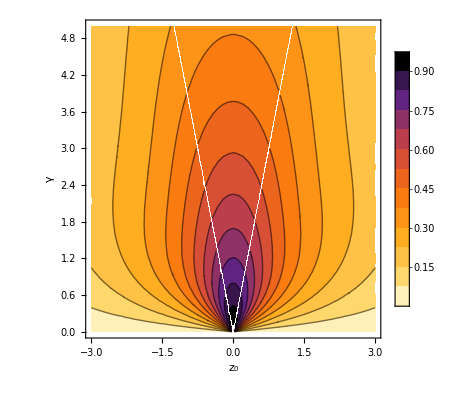

```mathematica
Δt = 1.0;
norma[h_,γ_] =Sqrt[SI[[2]]^2+SI[[3]]^2];
rangex = 3;
rangey=5;
plot =ContourPlot[norma[h,γ],{h,-rangex,rangex},{γ,0,rangey},ColorFunction->{ColorData["SunsetColors"][(1-#)/1.1]&},Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(z\), \(0\)]\)",FontSize->16],Style["γ",FontSize->16]}, PlotRange->{{-rangex,rangex},{0,rangey}},BaseStyle->{FontSize->14},PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->16}],Contours->12]
```

```mathematica
widthSingleColumn=1063;(*https://writing.stackexchange.com/questions/21658/what-is-the-image-size-in-scientific-paper-if-indicated-as-a-single-1-5-or-2-c*)
dpi=300;
fileName=FileNameJoin[{NotebookDirectory[],"Fig1.png"}];
Export[fileName,plot,"ImageResolution"->dpi,ImageSize->widthSingleColumn]
```

## “A properly engineered QRC system” of Phys. Rev. E 107, 035306 with quadratic input

### Definitions

```mathematica
sx=PauliMatrix[1];sminus =  {{0,0},{1,0}};L1=sminus;H=h^2*sx/2;
```

### Computing p and q

```mathematica
Lindb[A_]:=-ⅈ(A.H-H.A) +γ*L1.A.ConjugateTranspose[L1]-(γ/2)*( ConjugateTranspose[L1].L1.A+A.ConjugateTranspose[L1].L1 ) ;
B=Table[PauliMatrix[i]/√2,{i,{4,1,2,3}}]; 
(*Este es el orden de la base del paper: I,x,y,z*)
L = Simplify[Table[Tr[B[[i]].Lindb[B[[j]]]],{i,1,4},{j,1,4}]]*Δt;
F= MatrixExp[L];
S = Table[Sum[F[[s,r]]*Tr[B[[r]].B[[a]].B[[s]].B[[b]]],{s,1,4},{r,1,4}],{a,1,4},{b,1,4}];
Kraus[X_] :=Sum[S[[a,b]]*(B[[a]].X.B[[b]]),{a,1,4},{b,1,4}] ;
W=FullSimplify[ Table[Tr[B[[i]].Kraus[B[[j]]]],{i,1,4},{j,1,4}],{h>0,Δt>0,γ>0}];
p = W[[2;;4,2;;4]];
q = W[[2;;4,1]];
p//MatrixForm
q//MatrixForm
```

(ⅇ^(-(γ Δt)/2) | 0 | 0
0 | ⅇ^(-(3 γ Δt)/4) (Cosh[1/4 √(-16 h^4+γ^2) Δt]+(γ Sinh[1/4 √(-16 h^4+γ^2) Δt])/(√(-16 h^4+γ^2))) | (4 ⅇ^(-(3 γ Δt)/4) h^2 Sinh[1/4 √(-16 h^4+γ^2) Δt])/(√(-16 h^4+γ^2))
0 | -(4 ⅇ^(-(3 γ Δt)/4) h^2 Sinh[1/4 √(-16 h^4+γ^2) Δt])/(√(-16 h^4+γ^2)) | ⅇ^(-(3 γ Δt)/4) (Cosh[1/4 √(-16 h^4+γ^2) Δt]-(γ Sinh[1/4 √(-16 h^4+γ^2) Δt])/(√(-16 h^4+γ^2))))

(0
(ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^2 γ (-3 γ √(-16 h^4+γ^2)+3 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) γ √(-16 h^4+γ^2)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) (-16 h^4+γ^2)+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) (-16 h^4+γ^2)))/(-32 h^8-14 h^4 γ^2+γ^4)
(ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) γ (8 h^4 √(-16 h^4+γ^2)-8 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^4 √(-16 h^4+γ^2)+γ^2 √(-16 h^4+γ^2)-ⅇ^(1/2 √(-16 h^4+γ^2) Δt) γ^2 √(-16 h^4+γ^2)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) γ (-16 h^4+γ^2)+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) γ (-16 h^4+γ^2)))/(2 (-32 h^8-14 h^4 γ^2+γ^4)))

### Computing the derivatives of p and q

```mathematica
dp = D[p,h];
dq = D[q,h];
MatrixForm[dp]MatrixForm[dq]
```

(0
-(ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^2 γ (-256 h^7-56 h^3 γ^2) (-3 γ √(-16 h^4+γ^2)+3 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) γ √(-16 h^4+γ^2)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) (-16 h^4+γ^2)+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) (-16 h^4+γ^2)))/((-32 h^8-14 h^4 γ^2+γ^4)^2)+(2 ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h γ (-3 γ √(-16 h^4+γ^2)+3 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) γ √(-16 h^4+γ^2)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) (-16 h^4+γ^2)+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) (-16 h^4+γ^2)))/(-32 h^8-14 h^4 γ^2+γ^4)+(8 ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^5 γ (-3 γ √(-16 h^4+γ^2)+3 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) γ √(-16 h^4+γ^2)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) (-16 h^4+γ^2)+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) (-16 h^4+γ^2)) Δt)/(√(-16 h^4+γ^2) (-32 h^8-14 h^4 γ^2+γ^4))+(ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^2 γ (128 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^3-64 (1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) h^3+(96 h^3 γ)/(√(-16 h^4+γ^2))-(96 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^3 γ)/(√(-16 h^4+γ^2))-48 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^3 γ Δt-16 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^3 √(-16 h^4+γ^2) Δt+16 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^3 √(-16 h^4+γ^2) Δt))/(-32 h^8-14 h^4 γ^2+γ^4)
-(ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) γ (-256 h^7-56 h^3 γ^2) (8 h^4 √(-16 h^4+γ^2)-8 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^4 √(-16 h^4+γ^2)+γ^2 √(-16 h^4+γ^2)-ⅇ^(1/2 √(-16 h^4+γ^2) Δt) γ^2 √(-16 h^4+γ^2)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) γ (-16 h^4+γ^2)+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) γ (-16 h^4+γ^2)))/(2 (-32 h^8-14 h^4 γ^2+γ^4)^2)+(4 ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^3 γ (8 h^4 √(-16 h^4+γ^2)-8 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^4 √(-16 h^4+γ^2)+γ^2 √(-16 h^4+γ^2)-ⅇ^(1/2 √(-16 h^4+γ^2) Δt) γ^2 √(-16 h^4+γ^2)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) γ (-16 h^4+γ^2)+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) γ (-16 h^4+γ^2)) Δt)/(√(-16 h^4+γ^2) (-32 h^8-14 h^4 γ^2+γ^4))+(ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) γ (128 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^3 γ-64 (1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) h^3 γ-(256 h^7)/(√(-16 h^4+γ^2))+(256 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^7)/(√(-16 h^4+γ^2))-(32 h^3 γ^2)/(√(-16 h^4+γ^2))+(32 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^3 γ^2)/(√(-16 h^4+γ^2))+32 h^3 √(-16 h^4+γ^2)-32 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^3 √(-16 h^4+γ^2)+128 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^7 Δt+16 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^3 γ^2 Δt-16 ⅇ^(1/2 √(-16 h^4+γ^2) Δt) h^3 γ √(-16 h^4+γ^2) Δt+16 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^3 γ √(-16 h^4+γ^2) Δt))/(2 (-32 h^8-14 h^4 γ^2+γ^4))) (0 | 0 | 0
0 | ⅇ^(-(3 γ Δt)/4) (-(8 h^3 γ Δt Cosh[1/4 √(-16 h^4+γ^2) Δt])/(-16 h^4+γ^2)+(32 h^3 γ Sinh[1/4 √(-16 h^4+γ^2) Δt])/((-16 h^4+γ^2)^(3/2))-(8 h^3 Δt Sinh[1/4 √(-16 h^4+γ^2) Δt])/(√(-16 h^4+γ^2))) | -(32 ⅇ^(-(3 γ Δt)/4) h^5 Δt Cosh[1/4 √(-16 h^4+γ^2) Δt])/(-16 h^4+γ^2)+(128 ⅇ^(-(3 γ Δt)/4) h^5 Sinh[1/4 √(-16 h^4+γ^2) Δt])/((-16 h^4+γ^2)^(3/2))+(8 ⅇ^(-(3 γ Δt)/4) h Sinh[1/4 √(-16 h^4+γ^2) Δt])/(√(-16 h^4+γ^2))
0 | (32 ⅇ^(-(3 γ Δt)/4) h^5 Δt Cosh[1/4 √(-16 h^4+γ^2) Δt])/(-16 h^4+γ^2)-(128 ⅇ^(-(3 γ Δt)/4) h^5 Sinh[1/4 √(-16 h^4+γ^2) Δt])/((-16 h^4+γ^2)^(3/2))-(8 ⅇ^(-(3 γ Δt)/4) h Sinh[1/4 √(-16 h^4+γ^2) Δt])/(√(-16 h^4+γ^2)) | ⅇ^(-(3 γ Δt)/4) ((8 h^3 γ Δt Cosh[1/4 √(-16 h^4+γ^2) Δt])/(-16 h^4+γ^2)-(32 h^3 γ Sinh[1/4 √(-16 h^4+γ^2) Δt])/((-16 h^4+γ^2)^(3/2))-(8 h^3 Δt Sinh[1/4 √(-16 h^4+γ^2) Δt])/(√(-16 h^4+γ^2))))

### Computing the fixed point x

```mathematica
D1=2;
D2=4;
ρ=Table[f[i,j],{i,D1},{j,D1}];
```

#### Computing the eigenvalues to take the one with zero value

```mathematica
Ltotal=Chop[-ⅈ(ρ.H-H.ρ) +γ*L1.ρ.ConjugateTranspose[L1]-(γ/2)*( ConjugateTranspose[L1].L1.ρ+ρ.ConjugateTranspose[L1].L1 ) ];
Do[Do[f[i,j]=Table[KroneckerDelta[(i-1) *D1+ j,k],{k,D2}],{j,D1}],{i,D1}];
Liouvillian=FullSimplify[Flatten[Ltotal,1]];
righteig=Chop[Eigenvectors[Liouvillian]];
Ei=Chop[Eigensystem[Liouvillian][[1]]];
index =FirstPosition[Ei,0];
```

#### Computing the x vector of the fixed point

```mathematica
w=Chop[righteig[[index[[1]]]]];
cont=1; (*variable contador*)
ρsteady=ConstantArray[0,{D1,D1}];
Do[ρsteady[[i,j]]= w[[cont]];cont=cont+1 ,{i,D1},{j,D1}];
ρsteady=FullSimplify[ρsteady/Tr[ρsteady],{h>0,γ>0}];
x = FullSimplify[Sqrt[2]*Table[Tr[B[[i]].ρsteady],{i,1,4}][[2;;4]],{h>0,γ>0}];
MatrixForm[ρsteady]MatrixForm[x]
```

(h^4/(2 h^4+γ^2) | (ⅈ h^2 γ)/(2 h^4+γ^2)
-(ⅈ h^2 γ)/(2 h^4+γ^2) | 1/(1+h^4/(h^4+γ^2))) (0
-(2 h^2 γ)/(2 h^4+γ^2)
-γ^2/(2 h^4+γ^2))

### Evaluating the Corollary

```mathematica
SI = FullSimplify[dp.x+dq,{h>0,γ>0}];
MatrixForm[SI]
```

(0
(2 ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h γ (γ^2 ((-1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) γ+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt)) √(-16 h^4+γ^2))-2 h^4 (5 (-1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) γ+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt)) √(-16 h^4+γ^2))))/(√(-16 h^4+γ^2) (2 h^4+γ^2)^2)
-(4 ⅇ^(-1/4 (3 γ+√(-16 h^4+γ^2)) Δt) h^3 γ (-4 (-1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) h^4+γ ((-1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)) γ+(1+ⅇ^(1/2 √(-16 h^4+γ^2) Δt)-2 ⅇ^(1/4 (3 γ+√(-16 h^4+γ^2)) Δt)) √(-16 h^4+γ^2))))/(√(-16 h^4+γ^2) (2 h^4+γ^2)^2))

### Numerical demonstration of nonzero Corollary vector

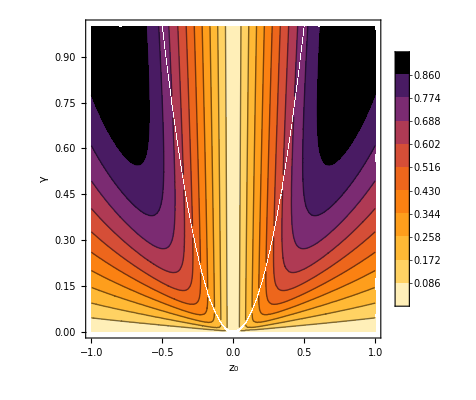

```mathematica
Δt = 1.0;
norma[h_,γ_] =Sqrt[SI[[2]]^2+SI[[3]]^2];
rangex = 1;
rangey=1.0;
plot =ContourPlot[norma[h,γ],{h,-rangex,rangex},{γ,0,rangey},ColorFunction->{ColorData["SunsetColors"][(1-#)/1.1]&},Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(z\), \(0\)]\)",FontSize->16],Style["γ",FontSize->16]}, PlotRange->{{-rangex,rangex},{0,rangey}},BaseStyle->{FontSize->14},PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->16}],Contours->10]
```

## Example with reset-rate as encoding

### Computing p and q for the reset-rate map

```mathematica
B=Table[PauliMatrix[i]/√2,{i,{4,1,2,3}}]; 
(*Matrix elements of σ*)
a = 1;
b = 0;
σ = {{a,b},{b,1-a}};
(*WE MUST GENERALIZE THE CHANNEL TO BE TRACE PRESERVING!!!*)
Reset[X_] := (1-ϵ)*X + ϵ*Tr[X]* σ;
(*Este es el orden de la base del paper: I,x,y,z*)
Wreset=FullSimplify[ Table[Tr[B[[i]].Reset[B[[j]]]],{i,1,4},{j,1,4}],{0<ϵ<1}];
preset =Wreset[[2;;4,2;;4]];
qreset = Wreset[[2;;4,1]];
MatrixForm[preset] MatrixForm[qreset]
```

(0
0
ϵ) (1-ϵ | 0 | 0
0 | 1-ϵ | 0
0 | 0 | 1-ϵ)

### Sanity check for the fixed point of the Reset rate map

```mathematica
id = {{1,0,0},{0,1,0},{0,0,1}};
x = FullSimplify[Inverse[id-preset].qreset,{0<ϵ<1}];
x2 = FullSimplify[Sqrt[2]*Table[Tr[B[[i]].σ],{i,1,4}][[2;;4]]];
MatrixForm[x]
MatrixForm[x2]
```

(0
0
1)

(0
0
1)

### Computing p and q for the depolarizing channel

```mathematica
id2 = PauliMatrix[4] ;
Dep[X_] := z*X +(1- z)*Tr[X]* id2;
(*Este es el orden de la base del paper: I,x,y,z*)
Wdep=FullSimplify[ Table[Tr[B[[i]].Dep[B[[j]]]],{i,1,4},{j,1,4}],{0<z<1}];
pdep =Wdep[[2;;4,2;;4]];
qdep= Wdep[[2;;4,1]];
MatrixForm[pdep] MatrixForm[qdep]
```

(0
0
0) (z | 0 | 0
0 | z | 0
0 | 0 | z)

### Computing p and q

```mathematica
p = preset.pdep;
q = preset.qdep +qreset;
MatrixForm[p] MatrixForm[q]
```

(0
0
ϵ) (z (1-ϵ) | 0 | 0
0 | z (1-ϵ) | 0
0 | 0 | z (1-ϵ))

### Computing the derivatives of p and q

```mathematica
dp = D[p,z];
dq = D[q,z];
MatrixForm[dp]MatrixForm[dq]
```

(0
0
0) (1-ϵ | 0 | 0
0 | 1-ϵ | 0
0 | 0 | 1-ϵ)

### Computing the fixed point x

```mathematica
id = {{1,0,0},{0,1,0},{0,0,1}};
x = FullSimplify[Inverse[id-p].q,{h>0,Δt>0,0<ϵ<1}];
MatrixForm[x]
```

(0
0
ϵ/(1+z (-1+ϵ)))

### Evaluating the Corollary

```mathematica
SI = FullSimplify[dp.x+dq];
MatrixForm[SI]
```

(0
0
((1-ϵ) ϵ)/(1+z (-1+ϵ)))

## Example with unitary as encoding

### Computing p and q for the reset-rate map

```mathematica
B=Table[PauliMatrix[i]/√2,{i,{4,1,2,3}}]; 
(*Matrix elements of σ*)
a = 1;
b = 0;
σ = {{a,b},{b,1-a}};
(*WE MUST GENERALIZE THE CHANNEL TO BE TRACE PRESERVING!!!*)
Reset[X_] := (1-ϵ)*X + ϵ*Tr[X]* σ;
(*Este es el orden de la base del paper: I,x,y,z*)
Wreset=FullSimplify[ Table[Tr[B[[i]].Reset[B[[j]]]],{i,1,4},{j,1,4}],{0<ϵ<1}];
preset =Wreset[[2;;4,2;;4]];
qreset = Wreset[[2;;4,1]];
MatrixForm[preset] MatrixForm[qreset]
```

(0
0
ϵ) (1-ϵ | 0 | 0
0 | 1-ϵ | 0
0 | 0 | 1-ϵ)

### Sanity check for the fixed point of the Reset rate map

```mathematica
id = {{1,0,0},{0,1,0},{0,0,1}};
x = FullSimplify[Inverse[id-preset].qreset,{0<ϵ<1}];
x2 = FullSimplify[Sqrt[2]*Table[Tr[B[[i]].σ],{i,1,4}][[2;;4]]];
MatrixForm[x]
MatrixForm[x2]
```

(0
0
1)

(0
0
1)

### Computing p and q for the unitary map

```mathematica
s=PauliMatrix[2];H=h*s/2;
Hamilt[A_]:=-ⅈ(A.H-H.A);
(*Este es el orden de la base del paper: I,x,y,z*)
L = Simplify[Table[Tr[B[[i]].Hamilt[B[[j]]]],{i,1,4},{j,1,4}]]*Δt;
F= MatrixExp[L];
S = Table[Sum[F[[s,r]]*Tr[B[[r]].B[[a]].B[[s]].B[[b]]],{s,1,4},{r,1,4}],{a,1,4},{b,1,4}];
KrausUnitary[X_] :=Sum[S[[a,b]]*(B[[a]].X.B[[b]]),{a,1,4},{b,1,4}] ;
Wunitary=FullSimplify[ Table[Tr[B[[i]].KrausUnitary[B[[j]]]],{i,1,4},{j,1,4}],{h>0,Δt>0}];
punitary =Wunitary[[2;;4,2;;4]];
qunitary = Wunitary[[2;;4,1]];
MatrixForm[punitary] MatrixForm[qunitary]
```

(0
0
0) (Cos[h Δt] | 0 | -Sin[h Δt]
0 | 1 | 0
Sin[h Δt] | 0 | Cos[h Δt])

### Computing p and q

```mathematica
p = preset.punitary;
q = preset.qunitary +qreset;
MatrixForm[p] MatrixForm[q]
```

(0
0
ϵ) ((1-ϵ) Cos[h Δt] | 0 | -((1-ϵ) Sin[h Δt])
0 | 1-ϵ | 0
(1-ϵ) Sin[h Δt] | 0 | (1-ϵ) Cos[h Δt])

### Computing the derivatives of p and q

```mathematica
dp = D[p,h];
dq = D[q,h];
MatrixForm[dp]MatrixForm[dq]
```

(0
0
0) (-Δt (1-ϵ) Sin[h Δt] | 0 | -Δt (1-ϵ) Cos[h Δt]
0 | 0 | 0
Δt (1-ϵ) Cos[h Δt] | 0 | -Δt (1-ϵ) Sin[h Δt])

### Computing the fixed point x

```mathematica
id = {{1,0,0},{0,1,0},{0,0,1}};
x = FullSimplify[Inverse[id-p].q,{h>0,Δt>0,0<ϵ<1}];
MatrixForm[x]
```

(((-1+ϵ) ϵ Sin[h Δt])/(2+(-2+ϵ) ϵ+2 (-1+ϵ) Cos[h Δt])
0
1/(2/ϵ+(-2+ϵ)/(1+(-1+ϵ) Cos[h Δt])))

### Evaluating the Corollary

```mathematica
SI = FullSimplify[dp.x+dq,{{h>0,Δt>0,b>0,a>0,0<ϵ<1}}];
MatrixForm[SI]
```

(0
-((-1+2 a) Δt (-1+ϵ) ϵ (-1+ϵ+Cos[h Δt]))/(2+(-2+ϵ) ϵ+2 (-1+ϵ) Cos[h Δt])
((-1+2 a) Δt (-1+ϵ) ϵ Sin[h Δt])/(2+(-2+ϵ) ϵ+2 (-1+ϵ) Cos[h Δt]))

### Numerical demonstration of nonzero Corollary vector

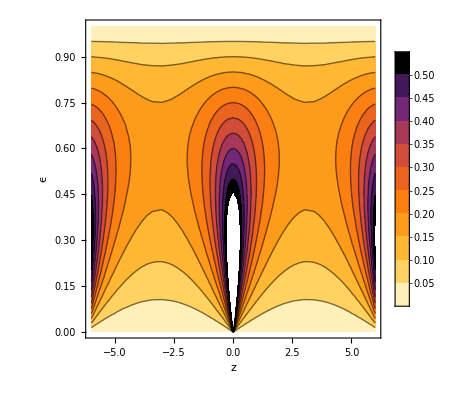

```mathematica
Δt = 1.0;
norma[h_,ϵ_] =Sqrt[SI[[2]]^2+SI[[3]]^2];
rangex = 6;
rangey=1.0;
(*The option ColorData["SunsetColors"][(1-#)/1.1]& reverses the color palette and doesn't take the whole spectrum, leaving outside the white.*)
plot =ContourPlot[norma[h,ϵ],{h,-rangex,rangex},{ϵ,0,rangey},ColorFunction->{ColorData["SunsetColors"][(1-#)/1.1]&},Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(z\), \(0\)]\)",FontSize->16],Style["ϵ",FontSize->16]}, PlotRange->{{-rangex,rangex},{0,rangey}},BaseStyle->{FontSize->14},PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->16}],Contours->10]
```